# 36: Lanczos Iteration

Arnoldi and all sorts of other stuff gets simpler for symmetric matrices. As you would expect Upper Hessenberg matrices become tridiagonal.  One other thing that happens is the general Arnoldi Iteration gets called Lanczos in the special symmetric case. Just as a reminder the Krylov space is 	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
and Arnoldi iteratively computes a nested sequence of orthonormal basis for the Krylov space (represented by orthogonal matrices Q_n∈ℝ^(m×n)) and a rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n) which represents the action of A on these basis through
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
The question is what simplifies when A is real symmetric.  We are going to look at the Arnoldi code and work out what can be tidied up.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Not surprisingly the Hessenberg matrix becomes “symmetric” tridiagonal. Since the top square is Symmetric the Ritz values are real.

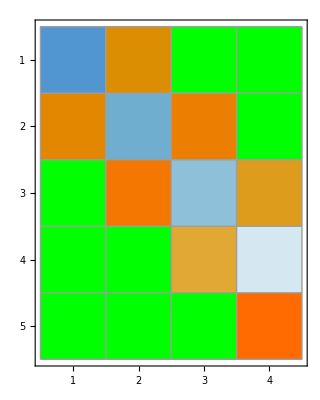

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
b=Normalize[RandomReal[{-1,1},m]];
{Q0,H0}={{b}ᵀ,{{}}};
{Q1,H1}=Arnoldi[A][{Q0,H0}];
{Q2,H2}=Arnoldi[A][{Q1,H1}];
{Q3,H3}=Arnoldi[A][{Q2,H2}];
{Q4,H4}=Arnoldi[A][{Q3,H3}];
MatrixPlot[Chop[H4],ColorRules->{0->Green},Mesh->All]
```

A glance at the code explains this simplification. By construction A.q_j∈Span(q_1,q_2,.…,q_j,q_(j+1)) and q_i.q_j=0 for i≠j with (again by construction) H_(i,j)=q_j.A.q_i . This means H_(i,j)=q_i.A.q_j=0 for i>j+1. If A is real symmetric i.e A=Aᵀ then 
	  H_(i,j)=q_i.A.q_j=q_j.Aᵀ.q_j=q_j.A.q_j=H_(j,i).
So elements of H more than one off the diagonal are zero while the sub and super diagonals match.  The Lanczos iteration incorporates this simplification and stores the diagonal entries α_n and off-diagonal entries β_n in vectors.

Working directly from Algorithm 36.1 I get the following as a manual start.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
(* Initialization *)
β0=0;
q1=Normalize[RandomReal[{-1,1},m]];
q0=0*q1;
(* n=1 *)
v=A.q1;
α1=q1.v;
v = v - β0 q0 - α1 q1;
β1=Norm[v];
q2=v/β1;
(* n=2 *)
v=A.q2;
α2=q2.v;
v = v - β1 q1 - α2 q2;
β2=Norm[v];
q3=v/β2;
```

The “zero” references are annoying in Mathematica, Julia, and Matlab!  I think the easiest fix is to view the n=1 step as part of the initialization.

```mathematica
LanczosInit[A_][q1_]:= Module[{v,α1,β1,q2},
v=A.q1;
α1=q1.v;
v = v - α1 q1;
β1=Norm[v];
q2=v/β1;
{{q1,q2}ᵀ,{{α1},{β1}}}
]
Lanczos[A_][{Q_,{α_,β_}}]:= Module[{m,n,qn,v,αn,βn,qNew},
{m,n}=Dimensions[Q];
qn=Q⟦All,n⟧;
v=A.qn;
αn=qn.v;
v=v-β⟦n-1⟧ Q⟦All,n-1⟧-αn qn;
βn=Norm[v];
qNew=v/βn;
{ArrayFlatten[({{Q, {qNew}ᵀ}})],{Append[α,αn],Append[β,βn]}}
]
```

Testing.  Note the preliminary initialization!

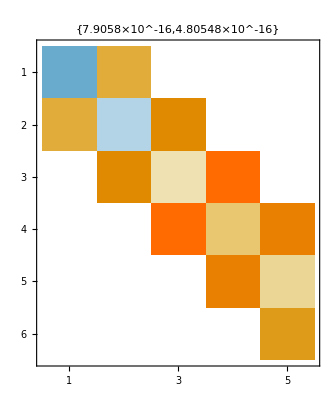

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=5;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
MatrixPlot[H,
PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}]]
```

## Symmetric Eigenvalue Problems with Lanczos.

All the operations for an iterative Krylov eigenvalue computation are faster for a Symmetric matrix:

The underlying Lanczos orthogonalization does not get slower as n grows. We can go longer without restarting.

Since eigenvalues and Ritz values are real there are only two big directions i.e. ±∞

The Ritz value computation is fast since the top square of H is symmetric tridiagonal.

### Easy Test

Lets see it work on a real matrix 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc1/bcsstk10.html

SparseArray[…]

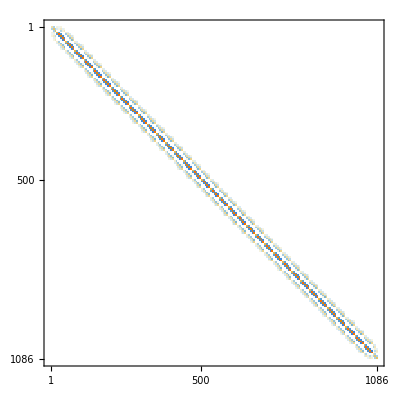

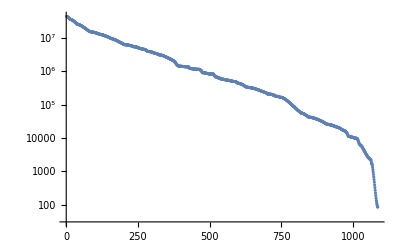

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk10.mtx.gz"]
MatrixPlot[A]
λs=Eigenvalues[Normal[A]];
ListLogPlot[λs]
```

We expect Lanczos to find the big eigenvalues and this is what the big ones look like!

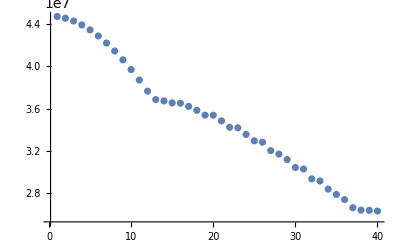

```mathematica
ListPlot[λs⟦1;;40⟧,
PlotRange->All]
```

Here is Lanczos

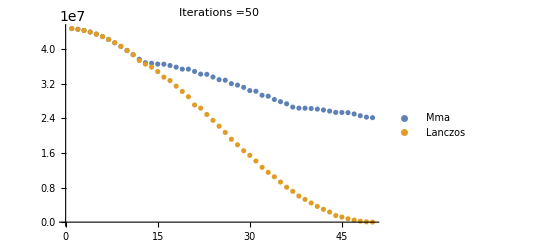

```mathematica
m=Length[A];
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=50;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
ListPlot[{
λs⟦1;;n⟧,
Eigenvalues[H⟦1;;n,1;;n⟧]
},
PlotLabel->StringForm["Iterations =``",n],
PlotLegends->{"Mma","Lanczos"}]
```

### Hard Test

Lets see it work on a hard real matrix 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/platz/plat1919.html

SparseArray[…]

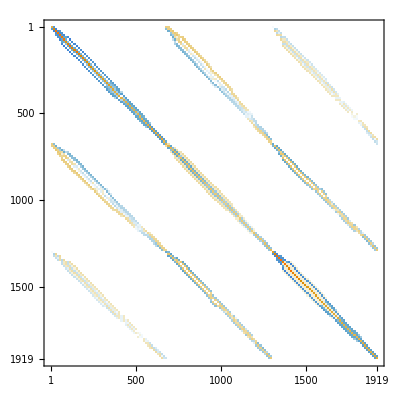

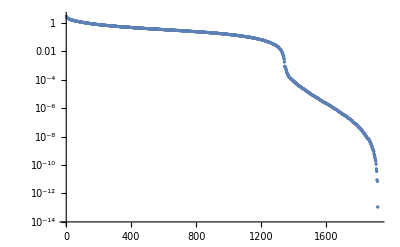

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/platz/plat1919.mtx.gz"]
MatrixPlot[A]
λs=Eigenvalues[Normal[A]];
ListLogPlot[λs]
```

We expect Lanczos to find the big eigenvalues and this is what the big ones look like!

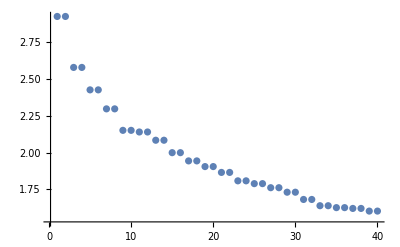

```mathematica
ListPlot[λs⟦1;;40⟧,
PlotRange->All]
```

This problem is in the test bank because these repeated eigenvalues make it hard for a simple Lanczos algorithm! It still finds eigenvalues but not always with the correct multiplicity!

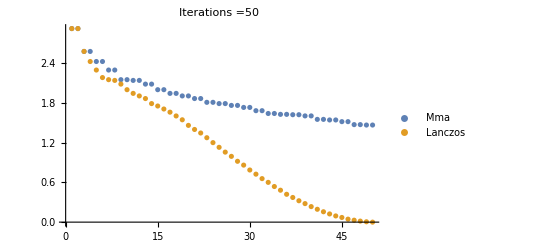

```mathematica
m=Length[A];
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=50;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
ListPlot[{
λs⟦1;;n⟧,
Eigenvalues[H⟦1;;n,1;;n⟧]
},
PlotLabel->StringForm["Iterations =``",n],
PlotLegends->{"Mma","Lanczos"}]
```

The Lanczos algorithm can miss duplicate eigenvalues.  Perhaps more disturbingly if you run it for a large number of steps it can find “ghost” eigenvalues that are extra copies!  The underlying problem is that the Q matrices can lose orthogonality. There are easy fixes! The easiest of all would be to use an Arnoldi solver that does a complete orthogonalization at every step rather than relying on the symmetry of A.

```mathematica
MatrixPlot[Qᵀ.Q,
PlotLegends->Automatic]
```

-Graphics-

## Bells and Whistles

Bells and whistles for Arnoldi include restarts and filters just like Arnoldi but now these include reorthogonalization and similar operations to accurately resolve eigenvalue multiplicity.